## Trayendo los datos de Python para visualizar las probabilidad de Viento/Demanda.

```mathematica
vientodemanda = Import["Viento_demanda_final.csv"]
```

{{Tiempo,Estado_demanda,Estado,Estado_viento_demanda,Nomenclatura},{2018-01-01 00:00:00,0.,2,2.,Regular/Baja},{2018-01-01 00:10:00,0.,2,2.,Regular/Baja},{2018-01-01 00:20:00,0.,2,2.,Regular/Baja},{2018-01-01 00:30:00,0.,2,2.,Regular/Baja},{2018-01-01 00:40:00,0.,2,2.,Regular/Baja},{2018-01-01 00:50:00,0.,2,2.,Regular/Baja},52548,{2018-12-31 23:00:00,0.,2,2.,Regular/Baja},{2018-12-31 23:10:00,,2,,},{2018-12-31 23:20:00,,2,,},{2018-12-31 23:30:00,,2,,},{2018-12-31 23:40:00,,2,,},{2018-12-31 23:50:00,,2,,}}
 |  |  |  |

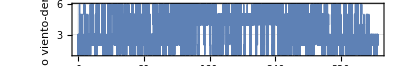

```mathematica
estadosvientodemanda= Table[{10  i/(60 24),vientodemanda[[i,4]]},{i,1,Length[vientodemanda]}];
VientoDemanda = ListLinePlot[estadosvientodemanda,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado viento-demanda"},PlotStyle->Thin, PlotRange->{All,{1,6}},ImageSize->Scaled[0.9],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->21]]
```

```mathematica
Export["VientoDemanda200.png",VientoDemanda]
```

VientoDemanda200.png

```mathematica
vientodemanda= vientodemanda[[All,4]][[2;;52555]];
transvientodemanda= Table[{vientodemanda[[i]],vientodemanda[[i+1]]},{i,1,Length[vientodemanda]-1}]
Probvientodemanda[i_,j_]:=Length[Select[transvientodemanda,#=={i,j}&]]/Length[Select[transvientodemanda,#[[1]]==i&]] 
Matrizvientodemanda= Table[Probvientodemanda[i,j],{i,1,6},{j,1,6}]
Matvientodemanda=Table[Probvientodemanda[i,j],{i,1,6},{j,1,6}]//MatrixForm
Matvientodemanda=Table[Probvientodemanda[i,j],{i,1,6},{j,1,6}]//MatrixForm // N
```

{{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,1.},{1.,1.},{1.,1.},{1.,2.},{2.,1.},{1.,1.},{1.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,1.},{1.,2.},{2.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,2.},{2.,1.},{1.,1.},52491,{3.,3.},{3.,3.},{3.,3.},{3.,3.},{3.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,2.},{2.,3.},{3.,2.},{2.,3.},{3.,2.},{2.,2.},{2.,3.},{3.,2.},{2.,2.}}
 |  |  |  |

{{695/836,127/836,2/1463,73/5852,17/5852,0},{455/5846,2372/2923,1169/11692,4/2923,97/11692,3/2923},{8/8021,1172/8021,520/617,1/8021,16/8021,64/8021},{57/6925,18/6925,0,5548/6925,1291/6925,11/6925},{12/13361,113/13361,16/13361,41/431,10730/13361,1219/13361},{0,2/1117,34/3351,8/3351,605/3351,2698/3351}}

(695/836 | 127/836 | 2/1463 | 73/5852 | 17/5852 | 0
455/5846 | 2372/2923 | 1169/11692 | 4/2923 | 97/11692 | 3/2923
8/8021 | 1172/8021 | 520/617 | 1/8021 | 16/8021 | 64/8021
57/6925 | 18/6925 | 0 | 5548/6925 | 1291/6925 | 11/6925
12/13361 | 113/13361 | 16/13361 | 41/431 | 10730/13361 | 1219/13361
0 | 2/1117 | 34/3351 | 8/3351 | 605/3351 | 2698/3351)

(0.83134 | 0.151914 | 0.00136705 | 0.0124744 | 0.00290499 | 0.
0.077831 | 0.811495 | 0.0999829 | 0.00136846 | 0.00829627 | 0.00102634
0.000997382 | 0.146116 | 0.842788 | 0.000124673 | 0.00199476 | 0.00797905
0.00823105 | 0.00259928 | 0. | 0.801155 | 0.186426 | 0.00158845
0.000898136 | 0.00845745 | 0.00119752 | 0.0951276 | 0.803084 | 0.0912357
0. | 0.00179051 | 0.0101462 | 0.00238735 | 0.180543 | 0.805133)

```mathematica
markovdiscreto=DiscreteMarkovProcess[{1,0,0,0,0,0},Matrizvientodemanda] //N
Graph[markovdiscreto,EdgeLabels->{DirectedEdge[i_,j_]:>MarkovProcessProperties[markovdiscreto,"TransitionMatrix"][[i,j]]}]
```

DiscreteMarkovProcess[{1,0,0,0,0,0},{{0.83134,0.151914,0.00136705,0.0124744,0.00290499,0.},{0.077831,0.811495,0.0999829,0.00136846,0.00829627,0.00102634},{0.000997382,0.146116,0.842788,0.000124673,0.00199476,0.00797905},{0.00823105,0.00259928,0.,0.801155,0.186426,0.00158845},{0.000898136,0.00845745,0.00119752,0.0951276,0.803084,0.0912357},{0.,0.00179051,0.0101462,0.00238735,0.180543,0.805133}}]

-Graphics-

```mathematica
markovdiscreto=DiscreteMarkovProcess[{1,0,0,0,0,0},Matrizvientodemanda] //N
ef[pts_List,e_]:={Arrowheads[{{0.015,0.65,Graphics@{Red,EdgeForm[Gray],Polygon[{{-1.5,-1},{1.6,0},{-1.5,1}}]}}}],Arrow[pts]}
g=Graph[markovdiscreto];
Scan[(PropertyValue[{g,#},EdgeLabels]=PropertyValue[{g,#},"Probability"])&];
Scan[(PropertyValue[{g,#},EdgeStyle]=Directive[GrayLevel[.7],Thickness[PropertyValue[{g,#},"Probability"]/15]])&,EdgeList[g]];
Scan[(PropertyValue[{g,#},EdgeShapeFunction]=ef)&,EdgeList[g]];
g
```

DiscreteMarkovProcess[{1,0,0,0,0,0},{{0.83134,0.151914,0.00136705,0.0124744,0.00290499,0.},{0.077831,0.811495,0.0999829,0.00136846,0.00829627,0.00102634},{0.000997382,0.146116,0.842788,0.000124673,0.00199476,0.00797905},{0.00823105,0.00259928,0.,0.801155,0.186426,0.00158845},{0.000898136,0.00845745,0.00119752,0.0951276,0.803084,0.0912357},{0.,0.00179051,0.0101462,0.00238735,0.180543,0.805133}}]

-Graphics-

```mathematica
vientonomenclatura = Import["Estados_viento_nomenclatura.csv"]
viento3estados= Table[{10  i/(60 24),vientonomenclatura[[i,2]]},{i,1,Length[vientonomenclatura]}];
viento3 = ListLinePlot[viento3estados,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado de viento grupal"},PlotStyle->Thin, PlotRange->{All,{1,3}}, ImageSize->Scaled[0.9],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20]]
```

```mathematica
dataviento2 = vientonomenclatura[[All,2]][[2;;52555]];
transviento2= Table[{dataviento2[[i]],dataviento2[[i+1]]},{i,1,Length[dataviento2]-1}]
Probviento2[i_,j_]:=Length[Select[transviento2,#=={i,j}&]]/Length[Select[transviento2,#[[1]]==i&]] 
Matrizviento2 = Table[Probviento2[i,j],{i,1,3},{j,1,3}]
Matviento2=Table[Probviento2[i,j],{i,1,3},{j,1,3}]//MatrixForm
Matviento2=Table[Probviento2[i,j],{i,1,3},{j,1,3}]//MatrixForm // N
```

```mathematica
demanda= Import["cadenademanda.csv"]
```

{{Tiempo,SIN},{2018-01-01 00:00:00,0},{2018-01-01 00:10:00,0},{2018-01-01 00:20:00,0},{2018-01-01 00:30:00,0},{2018-01-01 00:40:00,0},{2018-01-01 00:50:00,0},{2018-01-01 01:00:00,0},{2018-01-01 01:10:00,0},{2018-01-01 01:20:00,0},{2018-01-01 01:30:00,0},{2018-01-01 01:40:00,0},52532,{2018-12-31 21:10:00,0},{2018-12-31 21:20:00,0},{2018-12-31 21:30:00,0},{2018-12-31 21:40:00,0},{2018-12-31 21:50:00,0},{2018-12-31 22:00:00,0},{2018-12-31 22:10:00,0},{2018-12-31 22:20:00,0},{2018-12-31 22:30:00,0},{2018-12-31 22:40:00,0},{2018-12-31 22:50:00,0},{2018-12-31 23:00:00,0}}
 |  |  |  |

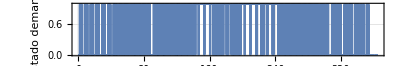

```mathematica
demandatable= Table[{10  i/(60 24),demanda[[i,2]]},{i,1,Length[demanda]}];
cadenademanda= ListLinePlot[demandatable,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado demanda"},PlotStyle->Thin,ImageSize->Scaled[0.9],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->21]]
```

```mathematica
Export["cadenademanda.png",cadenademanda]
```

cadenademanda.png

Tiempo de vida promedio

```mathematica
vientodemanda = Import["..\\Data\\ventosaestado.csv"] ;
secuencias = Split[vientodemanda[[All,2]],SameQ];
Tally[secuencias];
sumalistas=Total/@ secuencias;
Max[sumalistas];
totallistas=Table[{i,Count[sumalistas,i]},{i,1,Max[sumalistas]}];
totallistas2 = DeleteCases[totallistas,x_/;x[[2]]<1];

totallistas2[[All,2]]/Total[totallistas2[[All,2]]];
Total[totallistas2[[All,1]]*(totallistas2[[All,2]]/Total[totallistas2[[All,2]]])] /6 //N
```